```mathematica
num[c_]:=Numerator[c];den[c_]:=Denominator[c]
alpha[n_,c_]:=alpha[n,c]=den[c] (Floor[n/den[c]]-Floor[(n-1)/den[c]])-num[c] (Floor[n/num[c]]-Floor[(n-1)/num[c]])
F[n_,0,s_,c_]:=1
F[n_,1,s_,c_]:=If[n<s,0,(den[c] Floor[n/den[c]]-num[c] Floor[n/num[c]])-(den[c] Floor[(s-1)/den[c]]-num[c] Floor[(s-1)/num[c]])]
F[n_,k_,s_,c_]:=F[n,k,s,c]=Sum[If[alpha[m,c]==0,0,Binomial[k,j] alpha[m,c]^j F[Floor[n/(m^j)],k-j,m+1,c]],{j,1,k},{m,s,Floor[n^(1/k)]}]
E2Alt[n_,k_,c_]:=den[c]^-k F[n den[c]^k,k,den[c]+1,c]
E2[n_,k_,c_]:=E2[n,k,c]=(1/den[c])Sum[If[alpha[j,c]==0,0,alpha[j,c]E2[(den[c] n)/j,k-1,c]],{j,den[c]+1,den[c] n}];E2[n_,0,c_]:=1
E1[n_,z_,c_]:=Sum[Binomial[z,k] E2Alt[n,k,c],{k,0,Floor[Log[If[ c<2,c,2],n]]}]
E2x[n_,k_,x_]:=E2x[n,k,x]=Sum[E2x[n/j,k-1,x],{j,2,n}]-x Sum[E2x[n/(x j),k-1,x],{j,1,n/x}];E2x[n_,0,x_]:=1
E1x[n_,z_,c_]:=Sum[Binomial[z,k] E2x[n,k,c],{k,0,Floor[Log[If[ c<2,c,2],n]]}]
L2[n_,k_,c_]:=L2[n,k,c]=(1/den[c])Sum[If[alpha[j,c]==0,0,alpha[j,c] Log[j/den[c]]E2Alt[den[c] n/j,k-1,c]],{j,den[c]+1,den[c] n}];L2[n_,0,c_]:=1
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
L1[n_,z_,c_]:=L1[n,z,c]=Sum[bin[z,k] L2[n,k,c],{k,1,Floor[Log[If[ c < 2, c, 2],n]]}]
L2x[n_,1,b_]:=L2x[n,1,b]=L2x[n,1,b]=Sum[Log[j],{j,2,n}]-b Sum[Log[j b],{j,1,n/b}]
L2x[n_,k_,b_]:=L2x[n,k,b]=Sum[L2x[n/j,k-1,b],{j,2,n}]-b Sum[L2x[n/(j b),k-1,b],{j,1,n}]
L1x[n_,z_,x_]:=L1x[n,z,x]=Sum[bin[z,k] L2x[n,k,x],{k,1,Floor[Log[If[ x < 2, x, 2],n]]}]
```

```mathematica
DiscretePlot[D[  L1x[n,z,1.05],{z,1}]/.z->0, {n, 2, 100}]
```

$Aborted

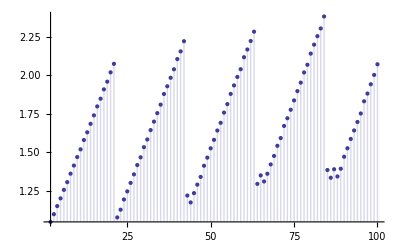

```mathematica
DiscretePlot[E1[n,-1,1.05], {n, 2, 100}]
```

```mathematica
N[L1x[10,-1,1.1]]
```

1.44615

```mathematica
ff[n_, c_] := -Sum[ Log[j] E1[ n/j, -1, c],{j,2,n}] + c Sum[ Log[ j c ] E1[n/(j c),-1, c],{j,1,Floor[n/c]}]
ff2[n_, c_] := -Sum[ Log[j] E1[ n/j, -1, c],{j,2,n}] + Sum[ c Log[ j c ] E1[n/(j c),-1, c],{j,2,Floor[n/c]}] + c Log[ c ] E1[n/(c),-1, c]
ff3[n_, c_] := -Sum[ Log[j] E1[ n/j, -1, c],{j,Floor[n/c]+1,n}] -Sum[ Log[j] E1[ n/j, -1, c],{j,2,Floor[n/c]}] + Sum[ c Log[ j c ] E1[n/(j c),-1, c],{j,2,Floor[n/c]}] + c Log[ c ] E1[n/(c),-1, c]
ff4[n_, c_] := c Log[ c ] E1[n/(c),-1, c] + Sum[ c Log[ j c ] E1[n/(j c),-1, c]-Log[j] E1[ n/j, -1, c],{j,2,Floor[n/c]}] -Sum[ Log[j] E1[ n/j, -1, c],{j,Floor[n/c]+1,n}]
ff4a[n_, c_] := c Log[ c ] E1[n/(c),-1, c]
ff4b[n_, c_] :=  Sum[ c Log[ j c ] E1[n/(j c),-1, c]-Log[j] E1[ n/j, -1, c],{j,2,Floor[n/c]}]
ff4c[n_, c_] := -Sum[ Log[j] E1[ n/j, -1, c],{j,Floor[n/c]+1,n}]
```

```mathematica
N[ff[ 10, 11/10]]
```

1.44615

```mathematica
N[ff4[ 10, 11/10]]
```

1.44615

```mathematica
N[ff4a[ 10, 11/10]]
```

2.56559

```mathematica
N[ff4b[ 10, 21/20]]
```

1.38471

```mathematica
N[ff4c[ 10, 21/20]]
```

-2.30259

```mathematica
$RecursionLimit=10000
xff[n_, c_] := -Sum[ Log[j] E1x[ n/j, -1, c],{j,2,n}] + c Sum[ Log[ j c ] E1x[n/(j c),-1, c],{j,1,Floor[n/c]}]
xff2[n_, c_] := -Sum[ Log[j] E1x[ n/j, -1, c],{j,2,n}] + Sum[ c Log[ j c ] E1x[n/(j c),-1, c],{j,2,Floor[n/c]}] + c Log[ c ] E1x[n/(c),-1, c]
xff3[n_, c_] := -Sum[ Log[j] E1x[ n/j, -1, c],{j,Floor[n/c]+1,n}] -Sum[ Log[j] E1x[ n/j, -1, c],{j,2,Floor[n/c]}] + Sum[ c Log[ j c ] E1x[n/(j c),-1, c],{j,2,Floor[n/c]}] + c Log[ c ] E1x[n/(c),-1, c]
xff4[n_, c_] := c Log[ c ] E1x[n/(c),-1, c] + Sum[ c Log[ j c ] E1x[n/(j c),-1, c]-Log[j] E1x[ n/j, -1, c],{j,2,Floor[n/c]}] -Sum[ Log[j] E1x[ n/j, -1, c],{j,Floor[n/c]+1,n}]
xff4a[n_, c_] := c Log[ c ] E1x[n/(c),-1, c]
xff4b[n_, c_] :=  Sum[ c Log[ j c ] E1x[n/(j c),-1, c]-Log[j] E1x[ n/j, -1, c],{j,2,Floor[n/c]}]
xff4bt[n_, c_] :=  Table[ c Log[ j c ] E1x[n/(j c),-1, c]-Log[j] E1x[ n/j, -1, c],{j,2,Floor[n/c]}]//TableForm
xff4c[n_, c_] := -Sum[ Log[j] E1x[ n/j, -1, c],{j,Floor[n/c]+1,n}]
```

10000

```mathematica
{N[xff4a[ nnn=10, rrr=1.02]], N[ xff4b[nnn,rrr]],N[xff4c[nnn,rrr]]}
```

{1.92275,1.58203,-2.30259}

2.30259

```mathematica
E1x[10/1.02,-1,1.02]
```

95.1919

```mathematica
Plot[ E1x[n,-1,1.1],{n,2,10}]
```

```mathematica
{ N[ xff4b[nnn=10,rrr=1.003]]}
```

{1.56292}

```mathematica
E1x[10,-1,1.1]
```

25.9184

```mathematica
E1x[9.5,-1,1.1]
```

15.4068

```mathematica
N[xff4bt[10,1.002]]
```

3.22147
2.65566
1.24994
0.997323
-1.12665
-1.51838
-1.8309
-2.08763

```mathematica
Em1[n_, y_] := 1 - Sum[ Em1[ n/j, y],{j,2,n}]+y Sum[ Em1[ n/(j y), y],{j,1,Floor[n/y]}]
Em1[n_, y_] := 1 - Sum[ Em1[ n/j, y],{j,2,n}]+y Sum[ Em1[ n/(j y), y],{j,2,Floor[n/y]}]+If[ n/y<1,0,y  Em1[ n/y, y]]
```

```mathematica
E1[10,-1,2]
```

3

```mathematica
Em1[10,2]
```

3

```mathematica
Limit[ 1+(n-2)(1-x)-x,x->1]
```

0